# Omicron US analysis: Plotting partitioned case counts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={"Pennsylvania","North Carolina"};
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
plottingStartDate="2021-11-01";
```

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-01-28

```mathematica
states=Union[seqData[[All,2]]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Alabama,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Dakota,Ohio,Oregon,South Carolina,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
stateVariantCounts[state_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==state&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
stateSequenceCounts[state_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==state][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->stateSequenceCounts[#][[-15;;-1]]&,states]
```

{Alabama→{{2022-01-14,15},{2022-01-15,31},{2022-01-16,17},{2022-01-17,31},{2022-01-18,22},{2022-01-19,4},{2022-01-20,0},{2022-01-21,6},{2022-01-22,5},{2022-01-23,2},{2022-01-24,6},{2022-01-25,0},{2022-01-26,0},{2022-01-27,0},{2022-01-28,0}},Arizona→{{2022-01-14,428},{2022-01-15,281},{2022-01-16,430},{2022-01-17,354},{2022-01-18,350},{2022-01-19,414},{2022-01-20,130},{2022-01-21,165},{2022-01-22,147},{2022-01-23,153},{2022-01-24,536},{2022-01-25,289},{2022-01-26,225},{2022-01-27,257},{2022-01-28,133}},Arkansas→{{2022-01-14,158},{2022-01-15,22},{2022-01-16,16},{2022-01-17,43},{2022-01-18,96},{2022-01-19,62},{2022-01-20,9},{2022-01-21,0},{2022-01-22,0},{2022-01-23,0},{2022-01-24,0},{2022-01-25,0},{2022-01-26,0},{2022-01-27,0},{2022-01-28,0}},California→{{2022-01-14,444},{2022-01-15,731},{2022-01-16,1000},{2022-01-17,1919},{2022-01-18,1236},{2022-01-19,383},{2022-01-20,355},{2022-01-21,189},{2022-01-22,1013},{2022-01-23,150},{2022-01-24,557},{2022-01-25,614},{2022-01-26,29},{2022-01-27,20},{2022-01-28,22}},Colorado→{{2022-01-14,438},{2022-01-15,476},{2022-01-16,517},{2022-01-17,168},{2022-01-18,386},{2022-01-19,1058},{2022-01-20,164},{2022-01-21,106},{2022-01-22,18},{2022-01-23,13},{2022-01-24,93},{2022-01-25,2},{2022-01-26,1},{2022-01-27,0},{2022-01-28,0}},Connecticut→{{2022-01-14,185},{2022-01-15,67},{2022-01-16,113},{2022-01-17,106},{2022-01-18,134},{2022-01-19,147},{2022-01-20,134},{2022-01-21,163},{2022-01-22,23},{2022-01-23,50},{2022-01-24,66},{2022-01-25,135},{2022-01-26,47},{2022-01-27,44},{2022-01-28,12}},Delaware→{{2022-01-14,60},{2022-01-15,34},{2022-01-16,26},{2022-01-17,51},{2022-01-18,72},{2022-01-19,50},{2022-01-20,29},{2022-01-21,22},{2022-01-22,1},{2022-01-23,1},{2022-01-24,0},{2022-01-25,0},{2022-01-26,0},{2022-01-27,0},{2022-01-28,0}},Florida→{{2022-01-14,268},{2022-01-15,200},{2022-01-16,126},{2022-01-17,116},{2022-01-18,238},{2022-01-19,247},{2022-01-20,76},{2022-01-21,29},{2022-01-22,19},{2022-01-23,14},{2022-01-24,18},{2022-01-25,15},{2022-01-26,16},{2022-01-27,0},{2022-01-28,0}},Georgia→{{2022-01-14,111},{2022-01-15,56},{2022-01-16,60},{2022-01-17,164},{2022-01-18,445},{2022-01-19,590},{2022-01-20,112},{2022-01-21,65},{2022-01-22,7},{2022-01-23,7},{2022-01-24,7},{2022-01-25,98},{2022-01-26,25},{2022-01-27,76},{2022-01-28,24}},Illinois→{{2022-01-14,49},{2022-01-15,43},{2022-01-16,46},{2022-01-17,113},{2022-01-18,175},{2022-01-19,132},{2022-01-20,27},{2022-01-21,17},{2022-01-22,9},{2022-01-23,13},{2022-01-24,48},{2022-01-25,22},{2022-01-26,16},{2022-01-27,1},{2022-01-28,2}},Indiana→{{2022-01-14,35},{2022-01-15,57},{2022-01-16,31},{2022-01-17,47},{2022-01-18,70},{2022-01-19,103},{2022-01-20,91},{2022-01-21,173},{2022-01-22,7},{2022-01-23,1},{2022-01-24,16},{2022-01-25,18},{2022-01-26,16},{2022-01-27,4},{2022-01-28,1}},Louisiana→{{2022-01-14,32},{2022-01-15,77},{2022-01-16,26},{2022-01-17,37},{2022-01-18,68},{2022-01-19,63},{2022-01-20,29},{2022-01-21,60},{2022-01-22,2},{2022-01-23,1},{2022-01-24,68},{2022-01-25,25},{2022-01-26,91},{2022-01-27,20},{2022-01-28,48}},Maryland→{{2022-01-14,77},{2022-01-15,63},{2022-01-16,57},{2022-01-17,64},{2022-01-18,153},{2022-01-19,119},{2022-01-20,82},{2022-01-21,68},{2022-01-22,34},{2022-01-23,15},{2022-01-24,11},{2022-01-25,15},{2022-01-26,18},{2022-01-27,14},{2022-01-28,7}},Massachusetts→{{2022-01-14,1037},{2022-01-15,372},{2022-01-16,397},{2022-01-17,844},{2022-01-18,758},{2022-01-19,698},{2022-01-20,747},{2022-01-21,419},{2022-01-22,402},{2022-01-23,943},{2022-01-24,1256},{2022-01-25,815},{2022-01-26,711},{2022-01-27,399},{2022-01-28,5}},Michigan→{{2022-01-14,96},{2022-01-15,59},{2022-01-16,65},{2022-01-17,88},{2022-01-18,81},{2022-01-19,59},{2022-01-20,42},{2022-01-21,22},{2022-01-22,6},{2022-01-23,4},{2022-01-24,21},{2022-01-25,5},{2022-01-26,5},{2022-01-27,0},{2022-01-28,0}},Minnesota→{{2022-01-14,107},{2022-01-15,33},{2022-01-16,77},{2022-01-17,100},{2022-01-18,797},{2022-01-19,105},{2022-01-20,76},{2022-01-21,61},{2022-01-22,133},{2022-01-23,43},{2022-01-24,44},{2022-01-25,23},{2022-01-26,9},{2022-01-27,0},{2022-01-28,0}},Nebraska→{{2022-01-14,51},{2022-01-15,44},{2022-01-16,62},{2022-01-17,70},{2022-01-18,119},{2022-01-19,51},{2022-01-20,83},{2022-01-21,68},{2022-01-22,43},{2022-01-23,5},{2022-01-24,96},{2022-01-25,82},{2022-01-26,66},{2022-01-27,63},{2022-01-28,31}},Nevada→{{2022-01-14,51},{2022-01-15,31},{2022-01-16,6},{2022-01-17,38},{2022-01-18,81},{2022-01-19,66},{2022-01-20,119},{2022-01-21,29},{2022-01-22,4},{2022-01-23,2},{2022-01-24,48},{2022-01-25,84},{2022-01-26,4},{2022-01-27,0},{2022-01-28,11}},New Hampshire→{{2022-01-14,88},{2022-01-15,40},{2022-01-16,44},{2022-01-17,25},{2022-01-18,43},{2022-01-19,25},{2022-01-20,28},{2022-01-21,17},{2022-01-22,5},{2022-01-23,9},{2022-01-24,75},{2022-01-25,25},{2022-01-26,16},{2022-01-27,13},{2022-01-28,0}},New Jersey→{{2022-01-14,182},{2022-01-15,30},{2022-01-16,27},{2022-01-17,91},{2022-01-18,181},{2022-01-19,354},{2022-01-20,1},{2022-01-21,7},{2022-01-22,6},{2022-01-23,3},{2022-01-24,14},{2022-01-25,100},{2022-01-26,57},{2022-01-27,18},{2022-01-28,0}},New Mexico→{{2022-01-14,93},{2022-01-15,18},{2022-01-16,17},{2022-01-17,49},{2022-01-18,94},{2022-01-19,122},{2022-01-20,116},{2022-01-21,16},{2022-01-22,6},{2022-01-23,5},{2022-01-24,2},{2022-01-25,0},{2022-01-26,2},{2022-01-27,0},{2022-01-28,0}},New York→{{2022-01-14,698},{2022-01-15,416},{2022-01-16,191},{2022-01-17,156},{2022-01-18,400},{2022-01-19,331},{2022-01-20,166},{2022-01-21,68},{2022-01-22,22},{2022-01-23,31},{2022-01-24,101},{2022-01-25,67},{2022-01-26,51},{2022-01-27,13},{2022-01-28,10}},North Dakota→{{2022-01-14,53},{2022-01-15,124},{2022-01-16,32},{2022-01-17,41},{2022-01-18,143},{2022-01-19,53},{2022-01-20,78},{2022-01-21,96},{2022-01-22,57},{2022-01-23,19},{2022-01-24,85},{2022-01-25,51},{2022-01-26,10},{2022-01-27,28},{2022-01-28,85}},Ohio→{{2022-01-14,86},{2022-01-15,23},{2022-01-16,24},{2022-01-17,19},{2022-01-18,118},{2022-01-19,82},{2022-01-20,85},{2022-01-21,106},{2022-01-22,3},{2022-01-23,0},{2022-01-24,90},{2022-01-25,25},{2022-01-26,35},{2022-01-27,46},{2022-01-28,48}},Oregon→{{2022-01-14,196},{2022-01-15,25},{2022-01-16,35},{2022-01-17,68},{2022-01-18,248},{2022-01-19,127},{2022-01-20,95},{2022-01-21,60},{2022-01-22,1},{2022-01-23,4},{2022-01-24,18},{2022-01-25,18},{2022-01-26,32},{2022-01-27,16},{2022-01-28,6}},South Carolina→{{2022-01-14,5},{2022-01-15,11},{2022-01-16,11},{2022-01-17,67},{2022-01-18,151},{2022-01-19,147},{2022-01-20,54},{2022-01-21,0},{2022-01-22,0},{2022-01-23,0},{2022-01-24,6},{2022-01-25,1},{2022-01-26,0},{2022-01-27,0},{2022-01-28,0}},Tennessee→{{2022-01-14,95},{2022-01-15,42},{2022-01-16,31},{2022-01-17,41},{2022-01-18,94},{2022-01-19,38},{2022-01-20,32},{2022-01-21,46},{2022-01-22,25},{2022-01-23,37},{2022-01-24,10},{2022-01-25,6},{2022-01-26,1},{2022-01-27,0},{2022-01-28,7}},Texas→{{2022-01-14,1090},{2022-01-15,662},{2022-01-16,365},{2022-01-17,83},{2022-01-18,205},{2022-01-19,190},{2022-01-20,488},{2022-01-21,408},{2022-01-22,475},{2022-01-23,306},{2022-01-24,79},{2022-01-25,63},{2022-01-26,56},{2022-01-27,0},{2022-01-28,0}},Utah→{{2022-01-14,225},{2022-01-15,227},{2022-01-16,19},{2022-01-17,382},{2022-01-18,402},{2022-01-19,394},{2022-01-20,248},{2022-01-21,237},{2022-01-22,79},{2022-01-23,24},{2022-01-24,53},{2022-01-25,0},{2022-01-26,0},{2022-01-27,0},{2022-01-28,1}},Vermont→{{2022-01-14,201},{2022-01-15,91},{2022-01-16,47},{2022-01-17,188},{2022-01-18,251},{2022-01-19,142},{2022-01-20,122},{2022-01-21,121},{2022-01-22,217},{2022-01-23,83},{2022-01-24,164},{2022-01-25,85},{2022-01-26,91},{2022-01-27,2},{2022-01-28,0}},Virginia→{{2022-01-14,17},{2022-01-15,3},{2022-01-16,8},{2022-01-17,29},{2022-01-18,280},{2022-01-19,182},{2022-01-20,0},{2022-01-21,0},{2022-01-22,0},{2022-01-23,1},{2022-01-24,2},{2022-01-25,0},{2022-01-26,3},{2022-01-27,0},{2022-01-28,0}},Washington→{{2022-01-14,196},{2022-01-15,49},{2022-01-16,47},{2022-01-17,127},{2022-01-18,357},{2022-01-19,170},{2022-01-20,69},{2022-01-21,58},{2022-01-22,40},{2022-01-23,54},{2022-01-24,152},{2022-01-25,380},{2022-01-26,124},{2022-01-27,45},{2022-01-28,23}},Wisconsin→{{2022-01-14,220},{2022-01-15,69},{2022-01-16,75},{2022-01-17,128},{2022-01-18,146},{2022-01-19,90},{2022-01-20,66},{2022-01-21,62},{2022-01-22,27},{2022-01-23,19},{2022-01-24,19},{2022-01-25,22},{2022-01-26,44},{2022-01-27,33},{2022-01-28,25}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[state_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==state,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.0001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{logitTransform[logitMinFreq],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{0,maxFreq}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[state_]:=Map[logisticPrevSeries[stateVariantCounts[state,#],stateSequenceCounts[state]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForStates=Map[freqForCountry,states];
```

```mathematica
modeledFreqsForStates=Map[{modeledLogisticPrevSeries[logisticPrevSeries[stateVariantCounts[#,"Omicron"],stateSequenceCounts[#]]]}&,states];
```

```mathematica
legendsForStates=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForStates];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[state_,variant_]:=Module[{stateVariantFrequencyDateSeries,stateCasesDateSeries,tuples},
stateVariantFrequencyDateSeries=smoothedPrevalence[stateVariantCounts[state,variant],stateSequenceCounts[state]];
stateCasesDateSeries=csGather[state];
tuples=compareWithDate[stateVariantFrequencyDateSeries,stateCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

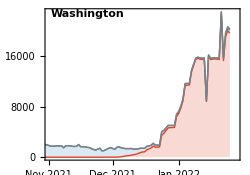

```mathematica
splitCasePlot["Washington"]
```

```mathematica
panels=Map[splitCasePlot,states];
```

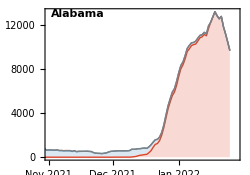
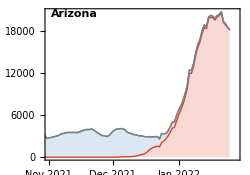
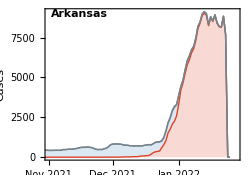
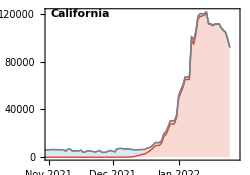
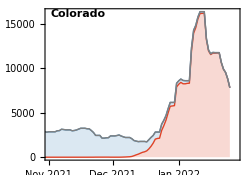
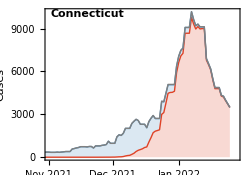
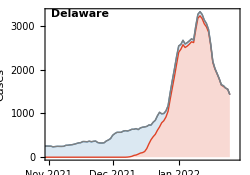
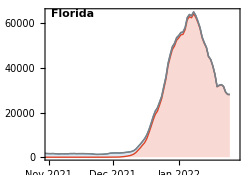
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=50000;
```

```mathematica
splitCaseLogPlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[state_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[state_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[state,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForStates=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,states];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{states,legendsForStates}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-log-cases.png